# PH20 Assignment 5

## Part 2

### Question 1

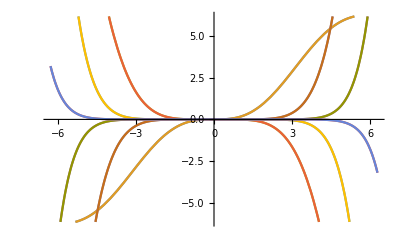

```mathematica
Clear[x,n, SerCos, SerSin]
SerCos[x_,n_]:=Normal[Series[Cos[y],{y,0,n}]]/.y->x;
SerSin[x_,n_]:=Normal[Series[Sin[y],{y,0,n}]]/.y->x;

(*Here is a manipulation plot to explore the convergence of approximations of sin and cos for different n *)

Manipulate[Plot[Evaluate[Table[function[x,n],n]],{x,-4π,4π}] , {n,1,25,2}, {function, {SerCos, SerSin}}]

(* Here is a plot which tests the difference between the difference between the series expansion and the actual value of sin *)

Plot[Evaluate[Table[SerSin[x,n]-Sin[x],{n,1,12,1}]],{x,-2π,2π}]
```

### Question 2

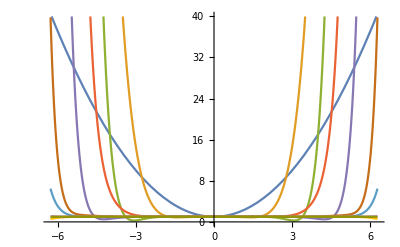

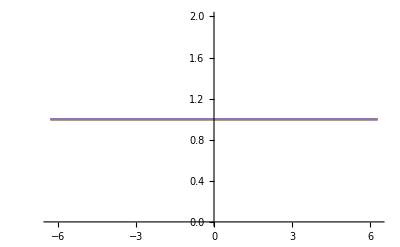

```mathematica
Clear[x,n, SerCos, SerSin]
(* As before *)
SerCos[x_,n_]:=Normal[Series[Cos[y],{y,0,n}]]/.y->x;
SerSin[x_,n_]:=Normal[Series[Sin[y],{y,0,n}]]/.y->x;

Plot[Evaluate[Table[SerSin[x,n]^2+SerCos[x,n]^2,{n,1,20,2}]],{x,-2π,2π}]

SerCosSq[x_,n_]:=Normal[Series[Cos[y]^2,{y,0,n}]]/.y->x;
SerSinSq[x_,n_]:=Normal[Series[Sin[y]^2,{y,0,n}]]/.y->x;

(* This produces a straight line at y = 1 as expected *)
Plot[Evaluate[Table[SerSinSq[x,n]+SerCosSq[x,n],{n,1,10,2}]],{x,-2π,2π}]
```

## Part 3

### Question 1

```mathematica
Rx[x_]:=({{1, 0, 0}, {0, Cos[x], -Sin[x]}, {0, Sin[x], Cos[x]}});
Rz[x_]:=({{Cos[x], -Sin[x], 0}, {Sin[x], Cos[x], 0}, {0, 0, 1}});
MatrixForm[Rx[θ]]
MatrixForm[Rx[ζ]]
MatrixForm [Rz[ϕ]]
```

(1 | 0 | 0
0 | Cos[θ] | -Sin[θ]
0 | Sin[θ] | Cos[θ])

(1 | 0 | 0
0 | Cos[ζ] | -Sin[ζ]
0 | Sin[ζ] | Cos[ζ])

(Cos[ϕ] | -Sin[ϕ] | 0
Sin[ϕ] | Cos[ϕ] | 0
0 | 0 | 1)

### Question 2

```mathematica
Rot3[ψ_,θ_,ϕ_]:=Rz[ψ].Rx[θ].Rz[ϕ]
MatrixForm[FullSimplify[Rot3[ψ,θ, ϕ]]]
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ψ]
Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[θ]
Sin[θ] Sin[ϕ] | Cos[ϕ] Sin[θ] | Cos[θ])

### Question 3

```mathematica
Rot3Inverse[ψ_,θ_,ϕ_]:=Rz[-ϕ].Rx[-θ].Rz[-ψ]
MatrixForm[Simplify[Rot3Inverse[ψ,θ,ϕ].Rot3[ψ,θ,ϕ]]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

### Question 4

```mathematica
MatrixForm[FullSimplify[Inverse[Rot3[ψ,θ,ϕ]].Rot3[ψ,θ,ϕ]]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

## Part 1

```mathematica
(* Solving a complicated gaussian integral for Quantum Mechanics *)

const = Sqrt[{m * Om}/(Pi * h)]

FullSimplify[Integrate[const * Exp[(-(m * Om))/(2 * h)* (2*x^2+2 * x *(q*Ene)/(m * Om^2) + ((q * Ene)/(m * Om^2))^2)],{x,-Infinity,Infinity}]]
```

{(√((m Om)/h))/(√π)}

{ConditionalExpression[ⅇ^(-(Ene^2 q^2)/(4 h m Om^3)),Re[(m Om)/h]>0]}

```mathematica
(* Diagonalizing a density matrix matrix in quantum statistical mechanics *)

mat={{1.,3.},{1.,2.}};vecs=Eigenvectors[mat];Inverse[Transpose[vecs]].mat.Transpose[vecs]//Chop//MatrixForm
```

(3.30278 | 0
0 | -0.302776)